```mathematica
axiom=Polygon[{{0,0},{1,0},{1,1},{0,1}}];

next[prev_]:=prev/.Polygon[{p1_,p2_,p3_, p4_}]:>{Polygon[{p1/3,p2/3,p3/3,p4/3}],Polygon[{p1/3+{1/3,0},p2/3+{1/3,0},p3/3+{1/3,0},p4/3+{1/3,0}}],
Polygon[{p1/3+{2/3,0},p2/3+{2/3,0},p3/3+{2/3,0},p4/3+{2/3,0}}],
Polygon[{p1/3+{0,1/3},p2/3+{0,1/3},p3/3+{0,1/3},p4/3+{0,1/3}}],
Polygon[{p1/3+{2/3,1/3},p2/3+{2/3,1/3},p3/3+{2/3,1/3},p4/3+{2/3,1/3}}],
Polygon[{p1/3+{0,2/3},p2/3+{0,2/3},p3/3+{0,2/3},p4/3+{0,2/3}}],
Polygon[{p1/3+{1/3,2/3},p2/3+{1/3,2/3},p3/3+{1/3,2/3},p4/3+{1/3,2/3}}],
Polygon[{p1/3+{2/3,2/3},p2/3+{2/3,2/3},p3/3+{2/3,2/3},p4/3+{2/3,2/3}}]};

draw[n_]:=Graphics[{EdgeForm[Yellow],Nest[next,N@axiom,n]}];
```

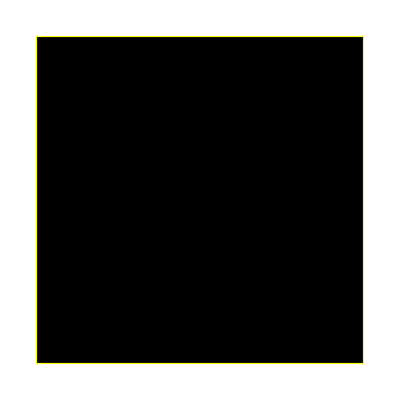

```mathematica
draw[0]
```

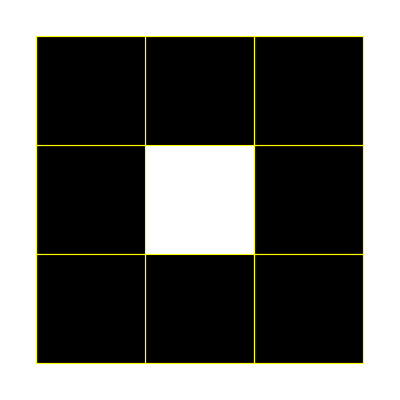

```mathematica
draw[1]
```

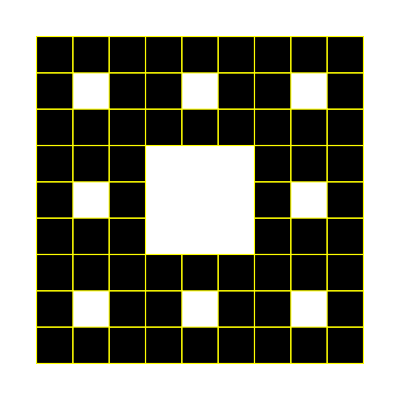

```mathematica
draw[2]
```

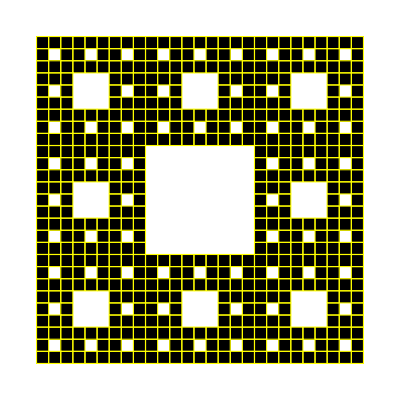

```mathematica
draw[3]
```

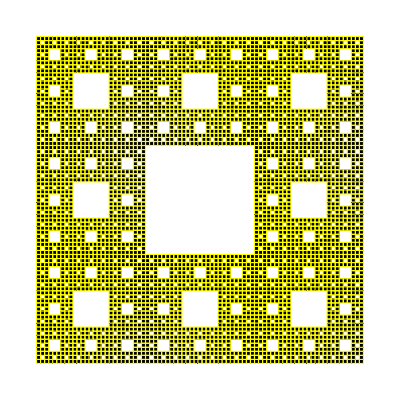

```mathematica
draw[4]
```

```mathematica
draw[5]
```

-Graphics-